```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
min= 10^-6;  max= 5; step=0.01;
```

```mathematica
Subscript[Ω, m0]=0.315;  H0.b2=(67.37)^2; Subscript[Ω, Λ0]= 0.6847; Subscript[Ω, r0]=  3 10^(-4);
```

```mathematica
β=0.69; α=1.0;
```

```mathematica
Subscript[Δ, e]=0.0; ;     legends={"Δ= 0","ΛCDM"};
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
Friedmann= (1+z)(B/2) y'[z] - A y[z]  + (  y[z] -Subscript[Ω, m0] H0.b2(1+z)^3 -Subscript[Ω, r0] H0.b2(1+z)^4  )^(2/(2-Δ)) ==0
```

-A y[z]+(-1429.7 (1+z)^3-1.36162 (1+z)^4+y[z])^(2/(2-Δ))+1/2 B (1+z) y'[z]==0

```mathematica
H2[Z_,alpha_,beta_,Delta_]:=NDSolveValue[{Friedmann, y[0]==H0.b2}/. {A-> alpha,B-> beta,Δ-> Delta} ,y[z],{z,0.0,Z},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10][[0]]
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

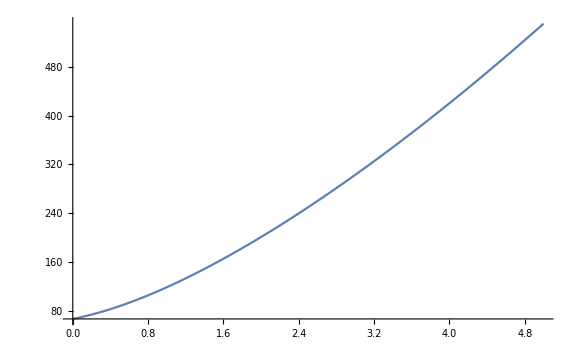

```mathematica
plotZvsH=Plot[Sqrt[H2[x,α,β,Subscript[Δ, e]][x]],{x,min,max}]
```

```mathematica
Z= Range[min,max,step];
```

```mathematica
H21=H2[Z,α,β,Subscript[Δ, e]];
```

```mathematica
H21[Z];
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
dH2dz[rango_,fun_]:=ND[fun[x],x,rango,WorkingPrecision->40,Terms->10];
```

```mathematica
dH2dz[Z,H2[Z,α,β,Subscript[Δ, e]]];
```

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
q[Z_,alpha_,beta_,Delta_]:=-1+(1/2)(1+Z)dH2dz[Z,H2[Z,alpha,beta,Delta]]/(H2[Z,alpha,beta,Delta][Z]) ;
```

```mathematica
dataZvsq1= Transpose[{Z,q[Z,α,β,Subscript[Δ, e]]}];
```

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

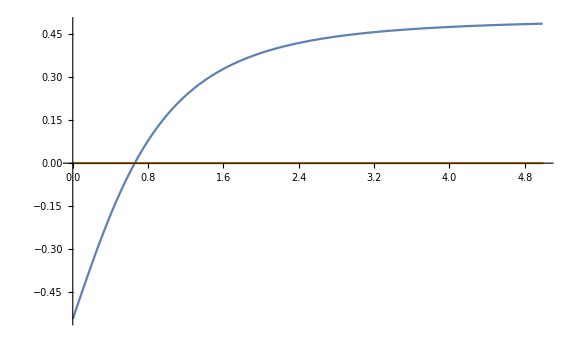

```mathematica
p1=ListLinePlot[{dataZvsq1,{{0,0},{5,0}}},PlotRange->All]
```

```mathematica
corte=Graphics`Mesh`FindIntersections@p1
```

{{0.658181,-1.92554×10^-16}}

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
rho[Z_,alpha_,beta_,Delta_]:= (1/H0.b2)(alpha H2[Z,alpha,beta,Delta][Z] - beta (1/2)(1+Z)dH2dz[Z,H2[Z,alpha,beta,Delta]])^(1-(Delta/2));
```

```mathematica
dataZvsDE1= Transpose[{Z,rho[Z,α,β,Subscript[Δ, e]]}];
```

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

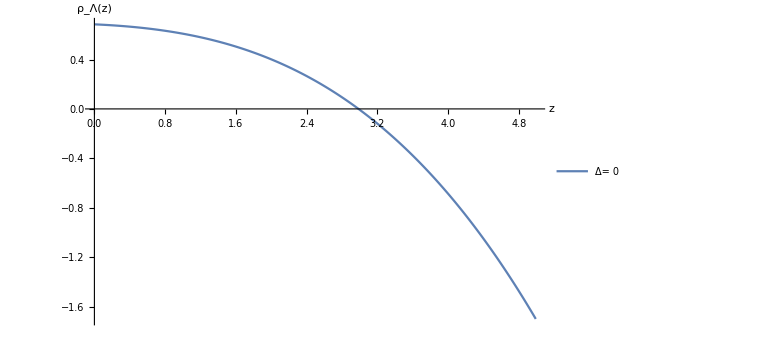

```mathematica
ListLinePlot[{dataZvsDE1}, AxesLabel->{"z","ρ_Λ(z)"},PlotRange->All,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,PlotLegends-> Placed[legends,{0.45,0.65}]]
```

```mathematica
DEz1=Interpolation[dataZvsDE1,Method->"Hermite"];
```

```mathematica
P[Z_,alpha_,beta_,Delta_]:=-rho[Z,alpha,beta,Delta]+ (1/3)(1+Z) ND[Interpolation[Transpose[{Z,rho[Z,alpha,beta,Delta]}],Method->"Hermite"][x],x,Z,WorkingPrecision->40,Terms->10]
```

```mathematica
dataZvsPDE1= Transpose[{Z,P[Z,α,β,Subscript[Δ, e]]}];
```

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

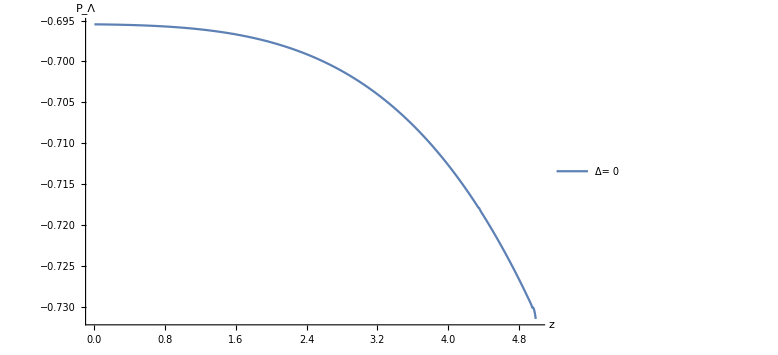

```mathematica
ListLinePlot[{dataZvsPDE1}, AxesLabel->{"z","P_Λ"},PlotRange->All,PlotLegends-> Placed[legends,{0.9,0.75}],LabelStyle->Directive[Black,Bold,10],ImageSize->Large]
```

```mathematica
w[Z_,alpha_,beta_,Delta_]:=P[Z,alpha,beta,Delta] /rho[Z,alpha,beta,Delta]
```

```mathematica
dataZvsWDE1= Transpose[{Z,w[Z,α,β,Subscript[Δ, e]]}];
```

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

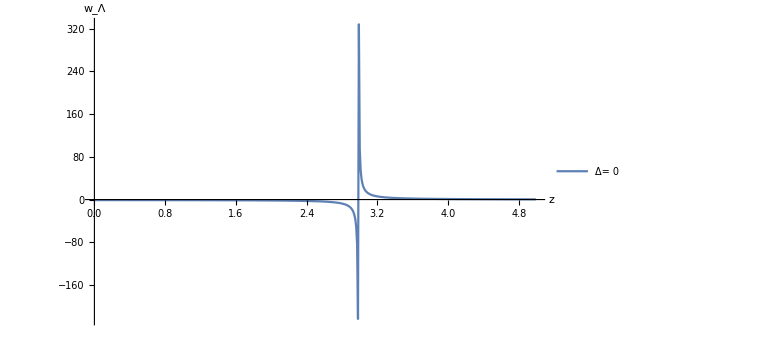

```mathematica
ListLinePlot[{dataZvsWDE1}, AxesLabel->{"z","w_Λ"},PlotRange->All,PlotLegends-> Placed[legends,{0.9,0.75}],LabelStyle->Directive[Black,Bold,10],ImageSize->Large]
```

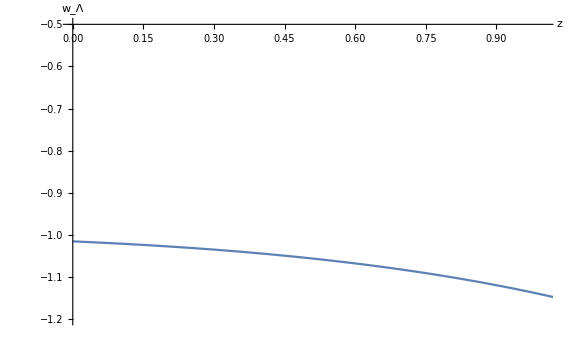

```mathematica
ListLinePlot[{dataZvsWDE1}, AxesLabel->{"z","w_Λ"},PlotRange->{{0,1},{-1.2,-0.5}},ImageSize->Large]
```

```mathematica
dataZvsWDE1[[1]]
```

{1.×10^-6,-1.01572}

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
zvs=Range[0,0.1,step]; vrho=Range[0.0,5,0.1];
```

```mathematica
vs2[Z_,alpha_,beta_,Delta_]:= ND[Interpolation[Transpose[{Z,P[Z,alpha,beta,Delta]}],Method->"Hermite"][x],x,Z,WorkingPrecision->40,Terms->10]/(ND[Interpolation[Transpose[{Z,rho[Z,alpha,beta,Delta]}],Method->"Hermite"][x],x,Z,WorkingPrecision->40,Terms->10]);
```

```mathematica
plotvs2={Transpose[{zvs,vs2[zvs,α,β,Subscript[Δ, e]]}]};
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

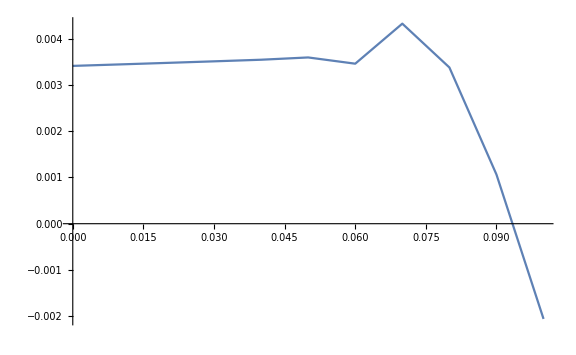

```mathematica
ListLinePlot[plotvs2, PlotRange-> All,PlotStyle->styles,LabelStyle->Directive[Black,Bold,10],ImageSize->Large]
```

```mathematica
vs2[zvs,α,β,Subscript[Δ, e]]
```

{0.00341337,0.00344561,0.00347849,0.00351213,0.0035468,0.00359621,0.00346116,0.00432717,0.00337972,0.0010636,-0.0020596}

```mathematica
vs2[zvs,0.93,0.45,0.0][[1]]
```

1.37524

```mathematica
DensityPlot[If[0≤(vs2[zvs,α,β,0.0][[1]])<1,0,1],{α,0.1,1.99},{β,0.1,1.99},LabelStyle->Directive[Black,Bold,11],PlotLegends->SwatchLegend[{RGBColor[38/255,84/255,138/255],RGBColor[255/255,242/255,191/255]},{"Estable","Inestable"}],FrameLabel->{"α","β","Δ = 0"},PlotPoints->150]
```

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

```mathematica
DensityPlot[If[0≤(vs2[zvs,α,β,1*10^-3][[1]])<1,0,1],{α,0.1,1.99},{β,0.1,1.99},LabelStyle->Directive[Black,Bold,10],PlotLegends->SwatchLegend[{RGBColor[38/255,84/255,138/255],RGBColor[255/255,242/255,191/255]},{"Estable","Inestable"}],FrameLabel->{"α","β","Δ = 1 x 10^-3"},PlotPoints->150]
```

```mathematica
DensityPlot[If[0≤(vs2[zvs,α,β,20*10^-3][[1]])<1,0,1],{α,0.1,1.99},{β,0.1,1.99},LabelStyle->Directive[Black,Bold,10],PlotLegends->SwatchLegend[{RGBColor[38/255,84/255,138/255],RGBColor[255/255,242/255,191/255]},{"Estable","Inestable"}],FrameLabel->{"α","β","Δ = 20 x 10^-3"},PlotPoints->150]
```

```mathematica
DensityPlot[If[0≤(vs2[zvs,α,β,50*10^-3][[1]])<1,0,1],{α,0.1,1.99},{β,0.1,1.99},LabelStyle->Directive[Black,Bold,10],PlotLegends->SwatchLegend[{RGBColor[38/255,84/255,138/255],RGBColor[255/255,242/255,191/255]},{"Estable","Inestable"}],FrameLabel->{"α","β","Δ = 50 x 10^-3"},PlotPoints->150]
```

```mathematica
DensityPlot[If[0<=(vs2[zvs,α,β,0.0][[1]])≤ 1&& (w[zvs,α,β,0.0][[1]])≤ -1/3 && (q[zvs,α,β,0.0][[1]])<0 && H2[100,α,β,0.0][100] >  H0.b2,0,1],{α,0.1,1.2},{β,0.1,1.2},LabelStyle->Directive[Black,Bold,11],PlotLegends->SwatchLegend[{RGBColor[38/255,84/255,138/255],RGBColor[255/255,242/255,191/255]},{"Allowed","Unallowed"}],FrameLabel->{"α","β","Δ = 0.0"},PlotPoints->200]
```

-Graphics-

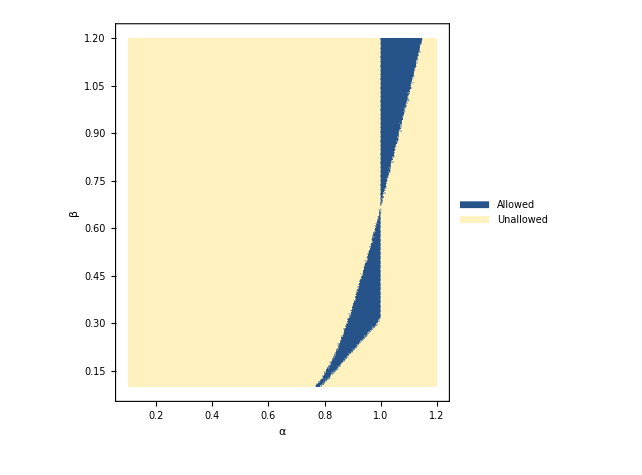

```mathematica
Del=50*10^-3; rho[vrho,α,β,Del][[-1]]
```

NDSolveValue::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

0.20667

```mathematica
N[Del]
```

0.05

```mathematica
DensityPlot[If[0<=(vs2[zvs,α,β,Del][[1]])≤ 1&& (w[zvs,α,β,Del][[1]])≤ -1/3 && (q[zvs,α,β,Del][[1]])<0,0,1],{α,0.25,1.35},{β,0.1,1.2},LabelStyle->Directive[Black,Bold,11],PlotLegends->SwatchLegend[{RGBColor[38/255,84/255,138/255],RGBColor[255/255,242/255,191/255]},{"Allowed","Unallowed"}],FrameLabel->{"α","β","Δ = 50 x 10^-3"},PlotPoints->200]
```

-Graphics-

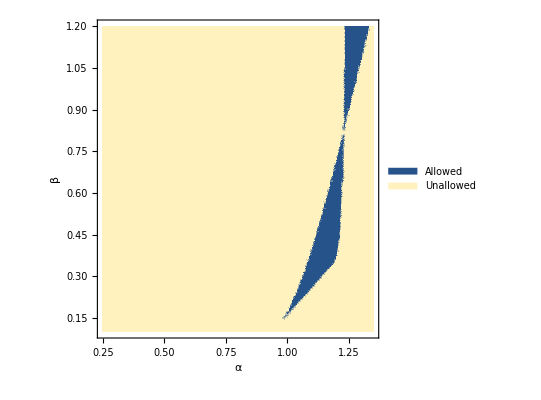

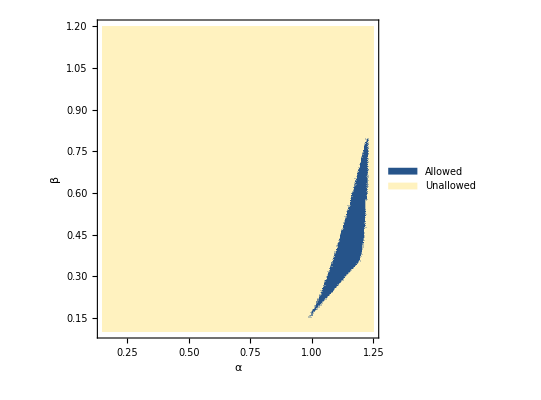

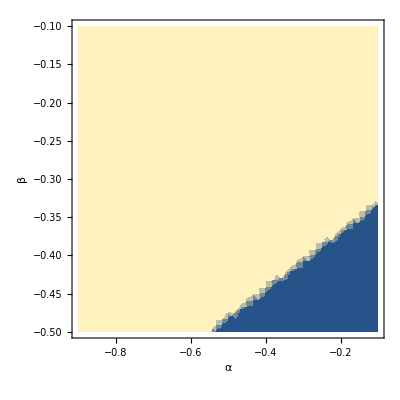

```mathematica
DensityPlot[If[0≤(vs2[zvs,α,β,0.0][[1]])<1,0,1],{α,-0.9,-0.1},{β,-0.5,-0.1},LabelStyle->Directive[Black,Bold,10],PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"0 ≤ c_s^2(α,β, z=0) < 1  →  0 "],Below],FrameLabel->{"α","β"},PlotPoints->25]
```

```mathematica
DensityPlot[{If[0≤(vs2[zvs,α,β,0.0][[1]]),1,0]*If[1≤(vs2[zvs,α,β,0.0][[1]]),2,1]},{α,0.1,1.99},{β,0.1,1.99},LabelStyle->Directive[Black,Bold,11],PlotLegends->SwatchLegend[{RGBColor[38/255,84/255,138/255],RGBColor[255/255,242/255,191/255]},{"Estable","Inestable"}],FrameLabel->{"α","β","Δ = 0"},PlotPoints->150]
```

-Graphics-